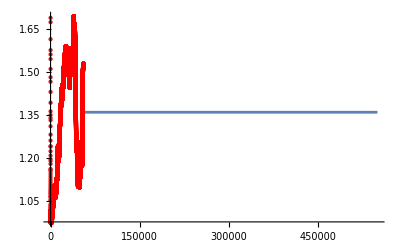

```mathematica
(* Read atmospheric 14C data*)
SetDirectory["/Users/yinonmb/Weizmann Institute Dropbox/YinonMoise Bar-On/git/soil_diskin/notebooks"];
C14DATADIR="../data/14C_atm_annot.csv";
C14DATA=Import[C14DATADIR, "HeaderLines"-> 1];
C14DATA= C14DATA[[All,{4,5}]];
(*Interpolate the 14C data, use the mean ratio for extrapolation*)
MeanR = Last[Mean[C14DATA[[-50000;;]]]];
atm14C=Interpolation[C14DATA,InterpolationOrder->0,"ExtrapolationHandler"-> {(MeanR&)}];

(* Plot the results of the interpolation to see it makes sense *)
Plot[atm14C[x],{x,0,550000},Epilog->{PointSize[Medium],Red,Point[C14DATA]}]
```

```mathematica
(* Define the function that calculates the radiocarbon signal from the inputs of the turnover time and mean age of the system *)
LognormalRadiocarbon[tau_,age_] := (
sig = Sqrt[Log[age/tau]];
mu = -Log[Sqrt[tau^3/age]];
r = NIntegrate[ atm14C[a]*Exp[-a/8267]* PDF[LogNormalDistribution[mu,sig],x] * Exp[-x*a] / Exp[-mu+(sig^2)/2],{x,0,Infinity},{a,0,Infinity}];
r
)

(* Define the function that optimizes the mean age for a given turnover time and observed radiocarbon signal *)
FindOptimalAge[tau_?NumericQ,rtrue_?NumericQ,InitialAge_?NumericQ]:=Module[{objectiveFunction,solution},(*Define the objective function to minimize:the squared difference between the function output and r_true*)objectiveFunction[age_?NumericQ]:=(LognormalRadiocarbon[tau,age]-rtrue)^2;
(*Use FindMinimum to find the age that minimizes the objective function*)(*FindMinimum requires a starting point for'age'*)solution=Quiet[FindMinimum[objectiveFunction[age],{age,InitialAge}]];
(*Return the value of age that minimizes the difference*)Return[age/. Last[solution]]]
```

```mathematica
(* Run code to optimize all of the site data in parallel *)

(*Ensure parallel kernels are launched (adjust number if needed,0 means all available)*)
LaunchKernels[];

(*3. Distribute definitions to parallel kernels*)
(*Make sure all symbols that FindOptimalAge and LognormalRadiocarbon depend on are distributed.*)
(*atm14C is already defined globally.If it were a more complex structure or function,you'd want to be sure it's available.*)
DistributeDefinitions[LognormalRadiocarbon,FindOptimalAge,atm14C];

(*4. Function to process a single row*)
ProcessRow[{tau_,rtrue_},defaultInitialAge_]:=Module[{optimalAge},Print["Processing: tau = ",tau,", r_true = ",rtrue];
optimalAge=FindOptimalAge[tau,rtrue,defaultInitialAge];
Return[optimalAge];
]
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

```mathematica
(*5. Main script*)
csvFilePath = "../results/tropical_sites_14C_turnover.csv"
Print["Importing data from: ",csvFilePath];
data=Import[csvFilePath,"CSV",HeaderLines->1];
(*data=data[{1},{"turnover","fm"}];*)
defaultInitialAge = 1000;
data = data[[{1,2,3},{7,6}]];
data=Import[csvFilePath,"Dataset",HeaderLines->1];
data = Values[data[[All,{"turnover","fm"}]]]//Normal;
results=ParallelMap[ProcessRow[#,defaultInitialAge]&,data]
```

../results/tropical_sites_14C_turnover.csv

Importing data from: ../results/tropical_sites_14C_turnover.csv

Processing: tau = 10.9002, r_true = 0.911312

Processing: tau = 20.8661, r_true = 0.822271

Processing: tau = 17.7759, r_true = 0.877755

Processing: tau = 17.5075, r_true = 0.889

Processing: tau = 17.4852, r_true = 0.882042

Processing: tau = 34.7018, r_true = 0.995694

Processing: tau = 5.5632, r_true = 0.951472

Processing: tau = 21.6687, r_true = 0.947984

Processing: tau = 11.3855, r_true = 0.894005

Processing: tau = 10.9673, r_true = 0.884773

Processing: tau = 5.61077, r_true = 0.92136

Processing: tau = 23.8838, r_true = 0.918634

Processing: tau = 11.2605, r_true = 0.922671

Processing: tau = 12.6938, r_true = 0.853911

Processing: tau = 10.6813, r_true = 0.841746

Processing: tau = 34.6131, r_true = 0.995694

Processing: tau = 12.2383, r_true = 0.884773

Processing: tau = 14.1328, r_true = 0.871388

Processing: tau = 11.3855, r_true = 0.894005

Processing: tau = 11.7076, r_true = 0.943756

Processing: tau = 8.98761, r_true = 0.887545

Processing: tau = 12.4168, r_true = 0.843955

Processing: tau = 15.1828, r_true = 0.889616

Processing: tau = 29.2665, r_true = 0.995694

Processing: tau = 13.4429, r_true = 0.822875

Processing: tau = 11.6565, r_true = 0.853911

Processing: tau = 11.7268, r_true = 0.884773

Processing: tau = 7.9129, r_true = 0.844676

Processing: tau = 21.597, r_true = 0.879691

Processing: tau = 3.39555, r_true = 0.853411

Processing: tau = 31.2575, r_true = 0.995694

Processing: tau = 19.2432, r_true = 0.889

Processing: tau = 14.2025, r_true = 0.94198

Processing: tau = 6.27878, r_true = 0.894676

Processing: tau = 10.2181, r_true = 0.94198

Processing: tau = 9.71448, r_true = 0.893458

Processing: tau = 10.8831, r_true = 0.850595

Processing: tau = 6.79786, r_true = 0.953867

Processing: tau = 7.84294, r_true = 0.827511

Processing: tau = 7.43038, r_true = 0.953867

Processing: tau = 14.9765, r_true = 0.946368

Processing: tau = 9.63614, r_true = 0.894676

Processing: tau = 6.40464, r_true = 0.894676

Processing: tau = 7.41648, r_true = 0.953867

Processing: tau = 10.3191, r_true = 0.919567

Processing: tau = 9.56115, r_true = 0.939581

Processing: tau = 11.91, r_true = 0.893458

Processing: tau = 18.1401, r_true = 0.845374

Processing: tau = 6.29619, r_true = 0.850319

Processing: tau = 17.9557, r_true = 0.781184

Processing: tau = 6.23161, r_true = 0.850319

Processing: tau = 21.6156, r_true = 0.990125

Processing: tau = 11.6148, r_true = 0.781184

Processing: tau = 13.3549, r_true = 0.894676

Processing: tau = 8.69454, r_true = 0.876959

Processing: tau = 10.2037, r_true = 0.953867

Processing: tau = 11.4782, r_true = 1.01459

Processing: tau = 10.786, r_true = 0.889199

Processing: tau = 9.64337, r_true = 0.958034

Processing: tau = 22.336, r_true = 0.986892

{11690.4,31986.8,57622.4,31044.,18970.1,42160.8,14768.1,36784.7,11771.3,12499.1,19586.1,12634.4,13958.,121120.,1590.22,1509.04,1510.98,1643.33,11010.,14684.9,11010.,11010.,6475.31,6488.36,15146.,15146.,17278.6,18039.,16811.2,28507.4,26897.,13550.6,11010.,43234.5,31510.7,23849.2,11010.,7209.51,21548.8,21822.1,16645.3,13547.9,16898.1,14853.7,11010.,7338.46,6987.86,6995.03,11010.,11010.,24062.2,121120.,121120.,121120.,64892.8,16960.,2190.03,2104.11,1809.42,11010.}

```mathematica
Export["../results/lognormal_site_parameters.csv",results,"CSV"]
```

```mathematica
CloseKernels[];
```

```mathematica
i= 54
LognormalRadiocarbon[data[[i,1]],results[[i]]]
LognormalRadiocarbon[data[[i,1]],85000]
results[[i]]
data[[i]]
```

54

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.76287 and 0.000518003 for the integral and error estimates.

0.76287

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.785226 and 0.000520448 for the integral and error estimates.

0.785226

121120.

{11.6148,0.781184}